```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
ω=1./GoldenRatio;
```

```mathematica
(* couplings *)
Clear[t];
t[i_,δ_]:=(1+δ (IntegerPart[ω (i+1)] - IntegerPart[ω i]))/(1+δ);
```

```mathematica
t[#,0.5]&/@Range[10]
```

{1.,0.666667,1.,1.,0.666667,1.,0.666667,1.,1.,0.666667}

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_,δ_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i,δ],{i,1,Fn-1}];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
h[6,0.5]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0.666667 | 0 | 0 | 0 | 0 | 0
0 | 0.666667 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0.666667 | 0 | 0
0 | 0 | 0 | 0 | 0.666667 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.666667
0 | 0 | 0 | 0 | 0 | 0 | 0.666667 | 0)

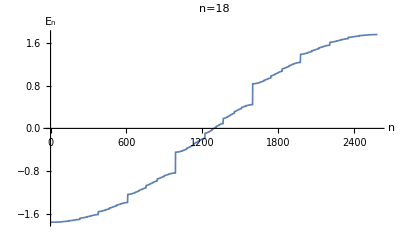

```mathematica
(* spectre *)
Block[{vp,plot,i=18},
vp=Sort[Eigenvalues[h[i,0.5]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
Export[dir<>"/data/spectrum_fibo_chain.png",plot];
Print[plot];
]
```

```mathematica
(* wavefunctions with standard labelling and IDoS *)
wf=Block[{val,vec,i=13,δ=0.9},
{val,vec}=Eigensystem[h[i,δ]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

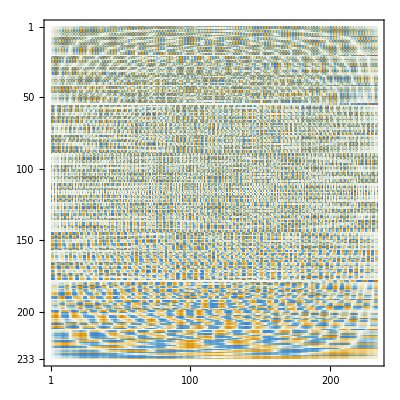

```mathematica
MatrixPlot [wf]
```